(-0.5 ⅇ^(-0.7 z3)-0.6106 (1-0.5 ⅇ^(-0.7 z3))-ω | (0.669065 (1-0.5 ⅇ^(-0.7 z3)) (0.5 ⅇ^(-0.7 zres)+0.6106 (1-0.5 ⅇ^(-0.7 zres))))/(1-0.5 ⅇ^(-0.7 zres))
0.36636 (1-0.5 ⅇ^(-0.7 z3)) (1-0.1 ω) | -0.241933 (1-0.5 ⅇ^(-0.7 z3))-ω)

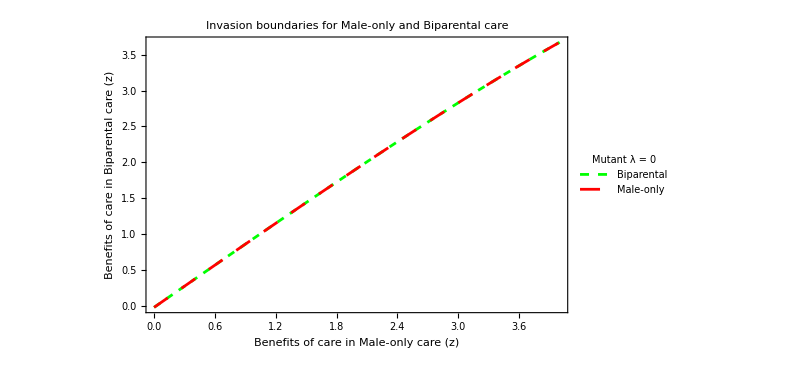

```mathematica
(*BASELINES*)
em0=0.5;
ef0 = 1-em0;

mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;

z0=1;
(*_________________________________________________________________________*)
(*RESIDENTS*)


(*Male only care*)
emres=em0;
efres =1-emres;

(*zres = z0;*)
cmres = 0.7;
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
wmres=1-((1-wm0)*E^(-cmres));
wfres= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres)));

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;

AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));





(*Biparental*)
emres3=em0;
efres3 =1-emres3;

(*zres3 = z0;*)
cmres3 = 0.35;
cfres3=0.35;
ctres3 = cmres3+cfres3;

mumres3=mum0*E^(-zres3*ctres3);
mufres3=muf0*E^(-zres3*ctres3);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres3=1-((1-mm0)*E^(-((1-mum0)*emres3)));
mfres3=1-((1-mf0)*E^(-((1-muf0)*efres3)));
KR3=k0;
rres3=rr0*E^(-((1-mum0)*emres3+((1-muf0)*efres3))/2);

wmres3=1-((1-wm0)*E^(-cmres3));
wfres3= 1-((1-wf0)*E^(-(efres3*(1-muf0)+(1-mum0)*emres3+cfres3)));

emmres3 = emres3*(1-mumres3)*mmres3;
emfres3 = efres3* (1-mufres3)*mfres3;
esmres3= emres3*(1-mumres3);
esfres3 = efres3* (1-mufres3);
amres3 = emres3*(1-mumres3)*mmres3*sigjmres;
afres3 = efres3* (1-mufres3)* mfres3*sigjfres;

AR3 =KR3*(1-((wmres3*amres3+wfres3*afres3)*(mumres3*emres3 + mufres3*efres3 + mmres3*esmres3 + mfres3*esfres3)/((emmres3*sigjmres+emfres3*sigjfres)*rres3*afres3)));



(*___________________________________________________*)
(*MUTANTS*)


(*Male only care*)
(*z=z0;*)
cm4=0.7;
cf4=0.0;
ct4 = cm4 + cf4;

mum4=mum0*E^(-z4*ct4);
muf4=muf0*E^(-z4*ct4);

em4=em0;
ef4 = 1-em4;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm4=1-((1-mm0)*E^(-((1-mum0)*em4)));
mf4=1-((1-mf0)*E^(-((1-muf0)*ef4)));
k4=k0; 
rr4=rr0*E^(-((1-mum0)*em4+((1-muf0)*ef4))/2);

wm4=1-((1-wm0)*E^(-cm4));
wf4=1-((1-wf0)*E^(-(ef4*(1-muf0)+(1-mum0)*em4 +cf4)));

emm4 = em4*(1-mum4)*mm4;
emf4 = ef4* (1-muf4)*mf4;
esm4= em4*(1-mum4);
esf4 = ef4*(1-muf4);
am4 = em4*(1-mum4)*mm4*sigjm;
af4= ef4* (1-muf4)* mf4*sigjf;



(*Biparental care*)
(*z=z0;*)
cm3=0.35;
cf3=0.35;
ct3 = cm3 + cf3;
ct3;

em3=em0;
ef3=1-em3;

mum3=mum0*E^(-z3*ct3);
muf3=muf0*E^(-z3*ct3);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm3=1-((1-mm0)*E^(-((1-mum0)*em3)));
mf3=1-((1-mf0)*E^(-((1-muf0)*ef3)));

wm3=1-((1-wm0)*E^(-cm3));
wf3=1-((1-wf0)*E^(-(ef3*(1-muf0)+(1-mum0)*em3 +cf3)));

emm3 = em3*(1-mum3)*mm3;
emf3 = ef3* (1-muf3)*mf3;
esm3 = em3*(1-mum3);
esf3 = ef3*(1-muf3);

k=k0;
rr3=rr0*E^(-((1-mum0)*em3+((1-muf0)*ef3))/2);

am3 = em3*(1-mum3)*mm3*sigjm;
af3 = ef3* (1-muf3)* mf3*sigjf;



(*INVASION MATRICIES*)


(*Invading Male only care*)

(*Biparental mutant *)
a3=-(mum3*em3+muf3*ef3+mm3*esm3+mf3*esf3);
b30 = rr3*af3*(1-(AR/k));
c3=emm3*sigjm*(1-ω*taum)+emf3*sigjf*(1-ω*tauf);
d3 = -(wm3*am3+wf3*af3);
mat30={{-ω+a3,b30},{c3,-ω+d3}};
MatrixForm[mat30]
ans30=Solve[Det[mat30]==0,ω];
res30=Max[ω/.ans30];




(*Male only mutant*)
a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4);
b03 = rr4*af4*(1-(AR3/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat03={{-λ+a,b03},{c,-λ+d}};
MatrixForm[mat03];
ans03=Solve[Det[mat03]==0,λ];
res03=Max[λ/.ans03];



resMiF=Table[zres=0.0+i/10;jo=
FindRoot[{res30==0},{z3,0.5,1}];{zres,z3/.jo},{i,0,40}];

(*Flip*)
resFiMflip=Table[z4=0.0+i/10;jo=
FindRoot[{res03==0},{zres3,0.5,1}];{z4,zres3/.jo},{i,0,40}];


ListPlot[{Re[resMiF],Re[resFiMflip]},
Joined -> {True, True},
Frame -> {True,True, False, False},
PlotLegends->LineLegend[{"Biparental", "Male-only"},
LegendLabel-> "Mutant λ = 0",
LegendMarkerSize->{20,20},
LabelStyle ->{FontSize->16}
],
FrameLabel->{Row[{Style["Benefits of care in",Black, 18], Style[" Male-only", Red, 18], Style[" care (z)",Black,18]}],Style[Rotate[Column[{"Benefits of care in",Row[{Style["Biparental", Green], Style[" care"]}],"(z)   "},Alignment-> Center], 270 Degree],18]},LabelStyle ->Black,
PlotLabel-> Style[Column[{"Invasion boundaries for", " Male-only and Biparental care", " "}, Alignment -> Center],22],LabelingSize->350,
ImageSize-> 600,
PlotStyle  -> {{Green, Dashing[0.009]}, {Red, Dashing[0.02]}},
BaseStyle -> FontSize -> 14]
```